```mathematica
xcoord[t_,rf_,rm_,rp_]:=(rf+rm)*Cos[t/rf]+rp*Cos[t/rf+t/rm]
ycoord[t_,rf_,rm_,rp_]:=(rf+rm)*Sin[t/rf]+rp*Sin[t/rf+t/rm]
```

```mathematica
xcoord[t_,rf_,rm_,rp_]:=(rf-rm)*Cos[t/rf]+rp*Cos[t/rf-t/rm]
ycoord[t_,rf_,rm_,rp_]:=(rf-rm)*Sin[t/rf]+rp*Sin[t/rf-t/rm]
```

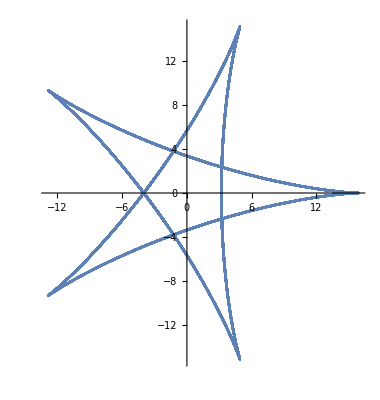

```mathematica
tf=100;
tm=40;
rf=tf/(2Pi);
rm=tm/(2 Pi);
rp=rm;
ParametricPlot[{xcoord[t,rf,rm,rp],ycoord[t,rf,rm,rp]},{t,0,10000}]
```

```mathematica
Manipulate[ParametricPlot[{xcoord[t,rf,rm,rp],ycoord[t,rf,rm,rp]},{t,0,LCM[rf,rm]*2 Pi}],{rf,1,100,1},{rm,1,100,1},{rp,1,100,1}]
```